## Area-Example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.5 (6-Nov-2012)) loaded Thu 8 Nov 2012 18:20:17
using xCellerator 0.90 and XSSA 1204002

```mathematica
poly={{0,0}, {1,0}, {5,1}, {1, 3}};
```

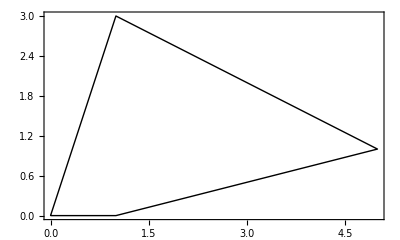

```mathematica
Show[Graphics[Line[AppendTo[poly, First[poly]]]], Frame-> True]
```

```mathematica
Area[poly]
```

15/2

```mathematica
w=TemplateRandomSquareGrid[9, {0,0}, {10,10}];
```

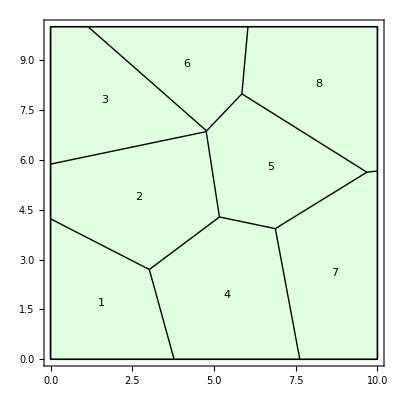

```mathematica
ShowTissue[w, Frame-> True, "CellNumbers"-> True]
```

```mathematica
Area[w]
```

{11.4847,14.5732,11.7024,14.9491,11.4584,8.65202,13.7324,13.4478}

```mathematica
Area[w,2]
```

14.5732